# Schijf LCA: Numeriek

Hier lost men het LCA probleem voor een schijf op aan de hand van NDEigensystem.

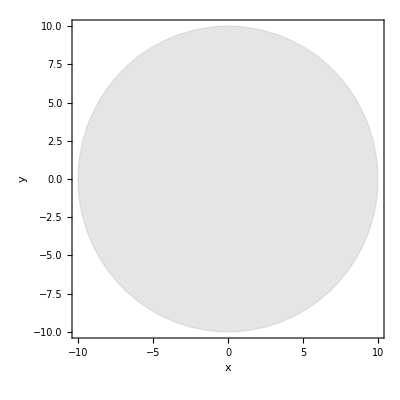

{{-4.05629×10^-17,0.0338997,0.0338997,0.0932858,0.0932859,0.146827,0.176514,0.176515,0.28282,0.282825},{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Ω = 1;
R = 10;
n = 10;

Graphics[{EdgeForm[Thin],Opacity[0.2],Gray,Disk[{0,0}, R]}, Frame->True,FrameTicks->{{{None,None},None},{{None,{R,"R"} },None}}, Axes->True, AxesLabel->{x,y}, PlotRange->Automatic]

{vals, funs} = NDEigensystem[{-Laplacian[u[x,y],{x,y}]+NeumannValue[0, {x,y} ∈ Circle[{0,0}, R]]}, u, {x,y} ∈ Disk[{0,0}, R], n]
Table[Plot3D[funs[[i]][x,y], {x,y} ∈ Disk[{0,0}, R], PlotRange->All, PlotLabel->vals[[i]]],{i,1,n}]
```

# Schijf: Coulomb

De eigenfuncties van het probleem in LCA kunnen opnieuw gebruikt worden om het probleem met de Coulomb potentiaal in te ontwikkelen.

```mathematica
Lm = ParallelTable[Ω^2 NIntegrate[(funs[[i]][x1,y1] Conjugate[funs[[j]][x2,y2]])/(√((x1-x2)^2 + (y1-y2)^2+(0.0001)^2)), {x1,y1} ∈  Disk[{0,0}, R],{x2,y2} ∈  Disk[{0,0}, R], PrecisionGoal->6,AccuracyGoal->6,Method->{"SymbolicDomainDecomposition",Method->{"GlobalAdaptive","MaxErrorIncreases"->7000}},MinRecursion->50,MaxRecursion->130, WorkingPrecision->15],{i,1,n},{j,1,n}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.46427600361808 and 0.138619531196631 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00368578160857333 and 0.110925326163726 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.011817446043674 and 0.10197832876899 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00065670180157345298851496847583035643356046900029106957505571569462 and 0.11308581497321763026612812134708467478095785186635131838082880826 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.003828062183334630724091869372506169615437042265425658464027613663 and 0.090004124051624770671059473375372685946504063789152785768440892591 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.004667882908148030442885638546729616940738591481872938078664952671 and 0.09242584620827763599878903120564313042433164426615428045471721749 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.023656339737667960086066627129566848054675659803111596199680555742 and 0.11224384269258044080735496373055582634264430548000673187598583962 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0118654328366996 and 0.098241471986606 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0149205268634694 and 0.0822063304890431 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0257944005438742 and 0.0891469722559453 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0045506712784997329766784029914060107174998303464217289508713759707 and 0.084491587804134225062382260234418574997052083355121428478644099795 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0092599809183403712569804071267944288605788167322496986287686709445 and 0.087929619503525901147488217105263742136366828968219469221896192199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0338714398443775 and 0.106830211263754 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0006567018015734529885149684758303508470235667173696879536353225459 and 0.11308581497321763026612812134708472111894516128092488250842310556 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3662615360920808751584898591341208624768596080730556380256793704 and 0.12012092041826856109700719779504159823533392377442192071302626943 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0109669190035194 and 0.0896012096644249 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.003702496922204249648013197916762902453190855536355253381399375864 and 0.091800075279499165370474590971886108702768475314701153522499331233 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.012226090472463210361355349403534528141606048011673413819974935664 and 0.090747759787609316357322324560678113041910134649567820557598948864 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{5.46427600361808,0.023656339737668,0.000656701801573453,-0.0281698617756439,0.00368578160857333,-0.487593750987355,-0.00382806218333463,-0.00449698383535946,0.011817446043674,-0.00466788290814803},{0.023656339737668,2.29803069577676,-0.0149205268634694,0.0250567025897059,0.0118654328366996,0.0124440251499959,0.00455067127849973,0.00927111345950032,0.0257944005438742,0.00925998091834037},{0.000656701801573453,-0.0149205268634694,2.36626153609208,0.0168041092224258,-0.0338714398443775,-0.00103752772616326,0.00370249692220425,-0.00530849389405735,-0.0109669190035194,0.0122260904724632},{-0.0281698617756439,0.0250567025897059,0.0168041092224258,1.53595143762585,-0.0136182344918272,-0.00383042998571966,-0.00709993551235137,-0.000492729849072885,-0.0130910294716043,-0.00950837053330958},{0.00368578160857333,0.0118654328366996,-0.0338714398443775,-0.0136182344918272,1.58098172728026,0.00210965933727209,0.0199792435029817,-0.0031898847190146,0.00460213356987802,0.00446826214197132},{-0.487593750987355,0.0124440251499959,-0.00103752772616326,-0.00383042998571966,0.00210965933727209,1.62558942386946,0.0031977859093665,-0.00283899050893782,0.00698442060552944,-0.00490992707697698},{-0.00382806218333463,0.00455067127849973,0.00370249692220425,-0.00709993551235137,0.0199792435029817,0.0031977859093665,1.19423585335921,-0.0113373994188981,0.0540220953604706,-0.00206920660391905},{-0.00449698383535946,0.00927111345950032,-0.00530849389405735,-0.000492729849072885,-0.0031898847190146,-0.00283899050893782,-0.0113373994188981,1.18952574052437,-0.0109098559352324,0.0351960886406796},{0.011817446043674,0.0257944005438742,-0.0109669190035194,-0.0130910294716043,0.00460213356987802,0.00698442060552944,0.0540220953604706,-0.0109098559352324,0.972052274894108,0.00031242549600254},{-0.00466788290814803,0.00925998091834037,0.0122260904724632,-0.00950837053330958,0.00446826214197132,-0.00490992707697698,-0.00206920660391905,0.0351960886406796,0.00031242549600254,0.957812421865875}}

```mathematica
Pm = Table[KroneckerDelta[i,j] vals[[i]], {i,1,n},{j,1,n}]
```

{{2.48577×10^-14,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,3.38997,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,3.38997,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,9.32856,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,9.32858,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,14.6826,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,17.6513,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,17.6513,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,28.2814,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,28.2819}}

```mathematica
Re[Eigenvalues[Pm.Lm]]
```

{30.0617,29.0508,24.7352,22.7822,22.6267,15.6226,15.2762,8.06339,8.04233,1.3145×10^-13}